## This notebook, calculates the frequency of a charged massles scalar field around a RN black hole considering a mirror: based on Phys Rev D 70 044039 (2004). Aveiro 20 feb 2013. check: mirrorFreq.mw

```mathematica
Exit
```

```mathematica
Clear; MaxExtraPrecision=100;
M=1;l=1; mu=0.1; qscal=0.3; Q=0.95;
```

```mathematica
winit=(0.15-0.00005*I)
```

0.15-0.00005 ⅈ

```mathematica
(*Define the Function of w as the solution of the Diferential equation given a value of r1, the position of the mirror. The returning value is the solution evaluated at r1 *)
```

```mathematica
LeavP1[w_?NumberQ]:=
Module[{Res},
r0=rp+10^(-8);r1=30; rm=M-Sqrt[M^2-Q^2]; rp=M+Sqrt[M^2-Q^2] ;wc=qscal*Q/rp;
qsol=-Sqrt[mu*mu-w*w] ;
rhosol=-I*rp^2*(w-wc)/(rp-rm);
sigmasol=(qscal*Q*w+M*mu^2-2*M*w^2);
sol=NDSolve[{(1-2*M/r+Q^2/r^2)*D[Rs[r],{r,2}]+(   2/r*( 1-2*M/r+Q^2/r^2) + (  2*M/r^2-2*Q^2/r^3  ) )*D[Rs[r],{r,1}]+(     1/(1-2*M/r+Q^2/r^2)*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2        )*Rs[r]==0,Rs[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(r0-rp)^(rhosol),Rs'[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(rhosol)*(r0-rp)^(rhosol-1)},Rs,{r,r0,r1},
          MaxSteps->50000];
Res=Rs[r1]/.sol];
```

```mathematica
(*Find the root of this function, this w is such as the value of the function is zero at *)
```

```mathematica
wres=FindRoot[LeavP1[w]==0,{w,winit}] [[1]][[2]]
```

0.183181+5.98258×10^-8 ⅈ

```mathematica
(*Check that the solution obtained is the solution wanted and plot it*)
```

```mathematica
r0=rp+10^(-8);r1=30; rm=M-Sqrt[M^2-Q^2]; rp=M+Sqrt[M^2-Q^2] ; wc=qscal*Q/rp
qsol=-Sqrt[mu*mu-wres*wres] ;
rhosol=-I*rp^2*(wres-wc)/(rp-rm);
sigmasol=(qscal*Q*wres+M*mu^2-2*M*wres^2);
(*potsol= 1/f*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2;*)
sol=NDSolve[{(1-2*M/r+Q^2/r^2)*D[Rs[r],{r,2}]+(   2/r*( 1-2*M/r+Q^2/r^2) + (  2*M/r^2-2*Q^2/r^3  ) )*D[Rs[r],{r,1}]+(     1/(1-2*M/r+Q^2/r^2)*(  wres-qscal*Q/r )^2-l*(l+1)/r^2-mu^2        )*Rs[r]==0,Rs[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(r0-rp)^(rhosol),Rs'[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(rhosol)*(r0-rp)^(rhosol-1)},Rs,{r,r0,r1},
          MaxSteps->50000];
```

0.217184

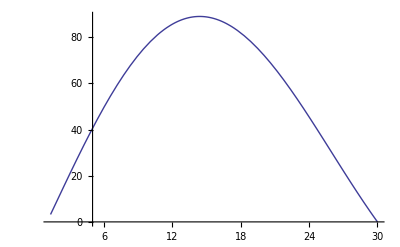

```mathematica
Plot[{2.01*Abs[Rs[r]/.sol]},{r,rp,r1}]
```

```mathematica
(*Now, do the previous procedure for several values of r1, the position of the mirror:
I approach the value from right and left because dont know the rate of change in the function,    in some cases is very high and then fails from one step to other.*)
```

```mathematica
winit=(0.15+0.000005*I);
ie=0;While[ie<151,NITMAX=250;
LeavP1[w_?NumberQ]:=
Module[{Res},
r0=rp+10^(-8);r1=30+ie/5; rm=M-Sqrt[M^2-Q^2]; rp=M+Sqrt[M^2-Q^2] ;wc=qscal*Q/rp;
qsol=-Sqrt[mu*mu-w*w] ;
rhosol=-I*rp^2*(w-wc)/(rp-rm);
sigmasol=(qscal*Q*w+M*mu^2-2*M*w^2);

sol=NDSolve[{(1-2*M/r+Q^2/r^2)*D[Rs[r],{r,2}]+(   2/r*( 1-2*M/r+Q^2/r^2) + (  2*M/r^2-2*Q^2/r^3  ) )*D[Rs[r],{r,1}]+(     1/(1-2*M/r+Q^2/r^2)*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2        )*Rs[r]==0,Rs[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(r0-rp)^(rhosol),Rs'[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(rhosol)*(r0-rp)^(rhosol-1)},Rs,{r,r0,r1},
          MaxSteps->50000];
Res=Rs[r1]/.sol];
wres=FindRoot[LeavP1[w]==0,{w,winit}] [[1]][[2]];
witer[ie]=wres;
radit[ie]=r1;
winit=wres-0.001;
ie=ie+1
]
t1r=Table[{N[radit[n],10],Re[witer[n]]},{n,0,150}];
t2r=Table[{N[radit[n],10],Im[witer[n]]},{n,0,150}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

{{30.,5.98259×10^-8},{30.2,5.92735×10^-8},{30.4,5.86941×10^-8},{30.6,5.80863×10^-8},{30.8,5.74677×10^-8},{31.,5.68278×10^-8},{31.2,5.61715×10^-8},{31.4,5.55023×10^-8},{31.6,5.48236×10^-8},{31.8,5.4133×10^-8},{32.,5.34442×10^-8},{32.2,5.27379×10^-8},{32.4,5.20278×10^-8},{32.6,5.13193×10^-8},{32.8,5.06067×10^-8},{33.,4.98948×10^-8},{33.2,4.91829×10^-8},{33.4,4.84734×10^-8},{33.6,4.77618×10^-8},{33.8,4.7058×10^-8},{34.,4.63558×10^-8},{34.2,4.56584×10^-8},{34.4,4.49637×10^-8},{34.6,4.42749×10^-8},{34.8,4.35922×10^-8},{35.,4.2915×10^-8},{35.2,4.22453×10^-8},{35.4,4.15811×10^-8},{35.6,4.09239×10^-8},{35.8,4.02727×10^-8},{36.,3.96301×10^-8},{36.2,3.89572×10^-8},{36.4,3.83673×10^-8},{36.6,3.77483×10^-8},{36.8,3.71373×10^-8},{37.,3.6532×10^-8},{37.2,3.59366×10^-8},{37.4,3.53492×10^-8},{37.6,3.47694×10^-8},{37.8,3.41987×10^-8},{38.,3.36358×10^-8},{38.2,3.30815×10^-8},{38.4,3.25356×10^-8},{38.6,3.19969×10^-8},{38.8,3.14677×10^-8},{39.,3.09455×10^-8},{39.2,3.04327×10^-8},{39.4,2.99269×10^-8},{39.6,2.94269×10^-8},{39.8,2.8939×10^-8},{40.,2.84637×10^-8},{40.2,2.7984×10^-8},{40.4,2.75172×10^-8},{40.6,2.70599×10^-8},{40.8,2.66108×10^-8},{41.,2.61648×10^-8},{41.2,2.57257×10^-8},{41.4,2.52994×10^-8},{41.6,2.48779×10^-8},{41.8,2.4464×10^-8},{42.,2.40562×10^-8},{42.2,2.36562×10^-8},{42.4,2.32621×10^-8},{42.6,2.28753×10^-8},{42.8,2.2495×10^-8},{43.,2.21218×10^-8},{43.2,2.17541×10^-8},{43.4,2.13931×10^-8},{43.6,2.10543×10^-8},{43.8,2.06902×10^-8},{44.,2.03482×10^-8},{44.2,2.0012×10^-8},{44.4,1.9681×10^-8},{44.6,1.93559×10^-8},{44.8,1.90368×10^-8},{45.,1.87259×10^-8},{45.2,1.84151×10^-8},{45.4,1.81141×10^-8},{45.6,1.78156×10^-8},{45.8,1.75233×10^-8},{46.,1.72356×10^-8},{46.2,1.69547×10^-8},{46.4,1.66836×10^-8},{46.6,1.64052×10^-8},{46.8,1.61386×10^-8},{47.,1.58758×10^-8},{47.2,1.56177×10^-8},{47.4,1.53643×10^-8},{47.6,1.51153×10^-8},{47.8,1.48708×10^-8},{48.,1.46304×10^-8},{48.2,1.43943×10^-8},{48.4,1.41623×10^-8},{48.6,1.39354×10^-8},{48.8,1.37104×10^-8},{49.,1.34908×10^-8},{49.2,1.32747×10^-8},{49.4,1.30624×10^-8},{49.6,1.28538×10^-8},{49.8,1.26493×10^-8},{50.,1.24476×10^-8},{50.2,1.22504×10^-8},{50.4,1.2074×10^-8},{50.6,1.18644×10^-8},{50.8,1.16766×10^-8},{51.,1.14925×10^-8},{51.2,1.13114×10^-8},{51.4,1.11333×10^-8},{51.6,1.09584×10^-8},{51.8,1.07865×10^-8},{52.,1.06174×10^-8},{52.2,1.04515×10^-8},{52.4,1.02885×10^-8},{52.6,1.01283×10^-8},{52.8,9.97074×10^-9},{53.,9.81596×10^-9},{53.2,9.66385×10^-9},{53.4,9.51434×10^-9},{53.6,9.36738×10^-9},{53.8,9.22296×10^-9},{54.,9.08084×10^-9},{54.2,8.94159×10^-9},{54.4,8.80439×10^-9},{54.6,8.66958×10^-9},{54.8,8.53707×10^-9},{55.,8.40235×10^-9},{55.2,8.28078×10^-9},{55.4,8.15296×10^-9},{55.6,8.03809×10^-9},{55.8,7.9077×10^-9},{56.,7.78816×10^-9},{56.2,7.67058×10^-9},{56.4,7.555×10^-9},{56.6,7.44133×10^-9},{56.8,7.32958×10^-9},{57.,7.21977×10^-9},{57.2,7.11176×10^-9},{57.4,7.00554×10^-9},{57.6,6.90126×10^-9},{57.8,6.79849×10^-9},{58.,6.69757×10^-9},{58.2,6.59826×10^-9},{58.4,6.50073×10^-9},{58.6,6.40457×10^-9},{58.8,6.31009×10^-9},{59.,6.22573×10^-9},{59.2,6.126×10^-9},{59.4,6.03618×10^-9},{59.6,5.94783×10^-9},{59.8,5.86092×10^-9},{60.,5.77548×10^-9}}

```mathematica
(*Calculate the values leftward*)
```

```mathematica
winit=(0.15+0.000005*I);
ie=0;While[ie<101,NITMAX=250;
LeavP1[w_?NumberQ]:=
Module[{Res},
r0=rp+10^(-8);r1=30-ie/5; rm=M-Sqrt[M^2-Q^2]; rp=M+Sqrt[M^2-Q^2] ;wc=qscal*Q/rp;
qsol=-Sqrt[mu*mu-w*w] ;
rhosol=-I*rp^2*(w-wc)/(rp-rm);
sigmasol=(qscal*Q*w+M*mu^2-2*M*w^2);
(*potsol= 1/f*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2;*)
sol=NDSolve[{(1-2*M/r+Q^2/r^2)*D[Rs[r],{r,2}]+(   2/r*( 1-2*M/r+Q^2/r^2) + (  2*M/r^2-2*Q^2/r^3  ) )*D[Rs[r],{r,1}]+(     1/(1-2*M/r+Q^2/r^2)*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2        )*Rs[r]==0,Rs[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(r0-rp)^(rhosol),Rs'[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(rhosol)*(r0-rp)^(rhosol-1)},Rs,{r,r0,r1},
          MaxSteps->50000];
Res=Rs[r1]/.sol];
wres=FindRoot[LeavP1[w]==0,{w,winit}] [[1]][[2]];
witer[ie]=wres;
radit[ie]=r1;
winit=wres+0.001;
ie=ie+1

]
t1l=Table[{N[radit[n],10],Re[witer[n]]},{n,0,100}];
t2l=Table[{N[radit[n],10],Im[witer[n]]},{n,0,100}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

```mathematica
(*The imaginary part vs the radius*)
```

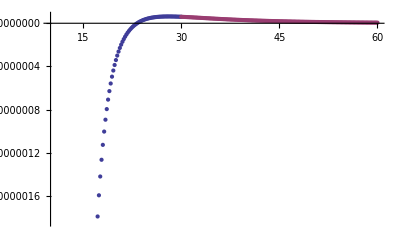

```mathematica
ListPlot[{t2l,t2r},Axes->True]
```

```mathematica
(*Real vs Radius*)
```

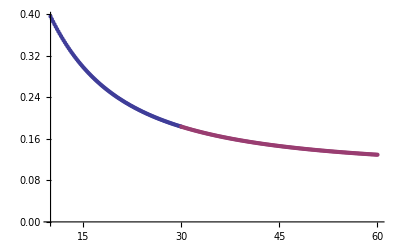

```mathematica
ListPlot[{t1l,t1r}]
```

```mathematica
Export["/home/h/skoli/pt/rnef/mathematica/mirror-radius/mu0.1/Q=0.95/q=0.3/R.dat",Join[t1l,t1r]]
Export["/home/h/skoli/pt/rnef/mathematica/mirror-radius/mu0.1/Q=0.95/q=0.3/I.dat",Join[t2l,t2r]]
```

/home/h/skoli/pt/rnef/mathematica/mirror-radius/mu0.1/Q=0.95/q=0.3/R.dat

/home/h/skoli/pt/rnef/mathematica/mirror-radius/mu0.1/Q=0.95/q=0.3/I.dat

```mathematica
(*This is for estimate the "Analytical" value using Cardoso's bomb *)
```

```mathematica
(*Radius*)
```

```mathematica
rp=M+Sqrt[M^2-Q^2]
rm=M-Sqrt[M^2-Q^2]
rmirror=40
```

1.6

0.4

40

```mathematica
(*Frequencies*)
```

```mathematica
wc=qscal*Q/rp
wtilde=(wa-wc)*(rp^2/(rp-rm))
```

0.45

2.13333 (-0.45+wa)

```mathematica
(*Nodes*)
```

```mathematica
n=0
```

0

```mathematica
(*First aproximation, the root of the Bessel function (has to be the n+1 root, otherwise the 1st is zero!)*)
```

```mathematica
jl12n=N[BesselJZero[l+1/2,n+1],10]
```

4.493409459

```mathematica
wfa=jl12n/rmirror
```

0.1123352365

```mathematica
(*Let's calculate the imaginary part, delta, we need some definitions in advance*)
```

```mathematica
Product[i^2+4*wtilde^2,{i,1,l}]
```

1+18.2044 (-0.45+wa)^2

```mathematica
gamm=(Factorial[l]/Factorial2[(2*l-1)])^2*rp^2*(rp-rm)^(2*l)/Factorial[2*l]/Factorial[2*l+1]*2/(2*l+1)*Product[i^2+4*wtilde^2,{i,1,l}]*jl12n^(2*l+1)
```

18.5805 (1+18.2044 (-0.45+wa)^2)

```mathematica
Dbess=D[BesselJ[l+1/2,x],x]/.x->jl12n
```

-0.367413504

```mathematica
f1=(-1)^(l)*BesselJ[-l-1/2,jl12n]/Dbess
```

1.049528

```mathematica
f2=(wfa-wc)/rmirror^(2*l+2)
```

-1.319×10^-7

```mathematica
(*Imaginary part delta*)
```

```mathematica
deltat=-gamm*f1*f2/.wa->wfa
```

7.91099×10^-6

```mathematica
(*make a list of the 1/r decay*)
```

```mathematica
tan=Table[jl12n/i,{i,50}];
```

```mathematica
(*Compare the behaviour of Re[w] in a plot*)
```



```mathematica
ListPlot[{t1l,t1r,tan}]
```